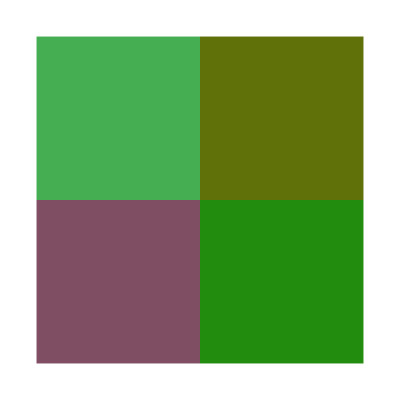

```mathematica
Testf[argl_]:=Module[{
GenerateBoard,
GenerateBoardField,
BoardComponents=Null,
BoardSize={0,0}
},
GenerateBoardField[x_,y_]:=Module[{},
BoardComponents[[x, y]]= {RandomColor[],Rectangle[{x*10,y*10},{x*10+10,y*10+10}]}
];
GenerateBoard[w_,h_]:=Module[{},
BoardSize={w,h};
BoardComponents=ConstantArray[Null,{w,h}];
For[x=1,x≤w,++x, 
For[y=1,y≤h,++y,
GenerateBoardField[x,y];
]
]
];
GenerateBoard[2,2];
Graphics[Flatten[BoardComponents]]
(*Show[
BoardComponents
]*)
];
Testf[0]
```